# Simulating Hybrid Electronic-Chemical Computer : Random Trajectories

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

In this Mathematica Notebook, we simulate a complete hybrid electronic-chemical computer using Secondary Current Distribution model together with resistance network model for the gel droplets placed on the electrode array. Using this formulation, we create random trajectories of setting pHs similar to what we observe in hybrid computation. We implement phosphate buffer dynamics model with droplets only interacting with current flow (using supporting electrolyte with higher electrophoretic mobilities) coupled with electrochemical reaction involving Hydroxyl ions on the electrode.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SeedRandom[111]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\

## Initializing Droplet Array based on Computational Problem Formulation

#### Physical Constants

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]];(* Vacuum Permittivity *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

#### Basic design and chemistry parameters

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

```mathematica
elecRadius=UnitConvert@Quantity[500.0,"μm"] ;(* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1000.0,"μm"];(* Gap between two nearby electrodes, defined from edge to edge *)
```

```mathematica
dropHeight=UnitConvert@Quantity[1000.0,"μm"]; (* Height of the droplet above electrode array *)
```

```mathematica
dropletVolume = UnitConvert[π(elecRadius+1/2 elecGap)^2 dropHeight,"m^3"];(* Volume of the droplet based on the height and electrode dimensions *)
```

```mathematica
CBack=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
ϵ0=UnitConvert@Quantity["VacuumPermittivity"];
```

```mathematica
ϵ=80.0; (* Dielectric Constrant of water *)
```

```mathematica
CDL=UnitConvert[Quantity[20.,"μF/cm^2"],"F/m^2"](* Assumed Typical Value inspired from Helmholtz Model 20μF/cm^2: Double Layer capacitance per unit area
https://edisciplinas.usp.br/pluginfile.php/4283018/mod_resource/content/1/Double_layer.pdf *)
```

0.2 F/m^2

```mathematica
𝒟=UnitConvert@Quantity[1.0 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[1.0 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction : Assumed value for the model (independent of Quinone electrochemistry) *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
n=1; (* Number of electrons involved in electrochemical reaction *)
```

```mathematica
λD=√((ϵ ϵ0 kB T)/(2 z^2 e^2 CBack NA)) (* Double Layer Length, 
Diffuse-charge dynamics in electrochemical systems, Bazant et al, Phys.Rev.E 70,021506,
https://doi.org/10.1103/PhysRevE.70.021506*)
```

9.70886×10^-10 m

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity for symmetric electrolyte, 
Diffuse-charge dynamics in electrochemical systems, Bazant et al, Phys.Rev.E 70,021506,
https://doi.org/10.1103/PhysRevE.70.021506 *)
```

0.751454 per meterper ohm

Using the bulk conductivity, we calculate the three resistances used in the local electrolyte-electrode pair model. These are just the basic approximations and can be updated with more details. 

1. R_B0=1/σ h/(π r^2) : This resistance connects the electrode to the height of the gel electrolyte (assumed). So, the length of the resistance is h and area is the area of the electrode π r^2. This is just an approximation to the vertical resistance from the electrode to center of the electrolyte, where we assume that the vertical current flows up to half the height.

2. R_B=1/σ r/(2 r h): This resistance is the horizontal resistance from the center of the electrode at the height h/2 to the edge of the electrode. So, the length of the resistance is the electrode radius and the area of the cross section is 2 r x h

3. R_B=1/σ g/(2 r h): This resistance is the horizontal resistance from  the edge of the one electrode to the edge of other electrode. So, the length of the resistance is the gap between two electrodes and the area of the cross section is 2 r x h

```mathematica
dropletBulkR0=1/BulkCond dropHeight/(π elecRadius^2)
```

1694.37 Ω

```mathematica
dropletBulkR=1/BulkCond elecRadius/(2 elecRadius dropHeight)
```

665.377 Ω

```mathematica
dropletBulkInt=1/BulkCond elecGap/(2 elecRadius dropHeight)
```

1330.75 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

7.57794×10^-6 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[FullSimplify[ j0[CEl,CEl,khom]],"A/m^2"]
```

24.1213 A/m^2

```mathematica
ExCurrentDensity/iLim
```

2.5

#### Phosphate Buffer Kinetics Parameters

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[20 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-8,"Molar"];
```

So, initial percent of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{0.0000385559,0.86316,0.136802,1.93237×10^-7}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{7.71119×10^-7 M,0.0172632 M,0.00273603 M,3.86475×10^-9 M}

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50; (* Necessary for better precision for numerical stability in pH calculations *)
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Input Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(n dropletVolume F)];  
(*Print[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q]];*)
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

#### Governing equations for multi-electrode array network

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ]) (* Time dependent potential shift function *)
```

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==If[electrodeType⟦i,j⟧=="ACTIVE", AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa n F ηm)/(R T)]-Exp[-(αc n F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]],leakageCurrent];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];

eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕPW1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕPS"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕPE"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕPN"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
Clear[λ,tS,cAdroplet,cBdroplet,cCdroplet,cDdroplet,soln,solnS]
```

```mathematica
If[FileExistsQ[baseDirectory<>"LOG.txt"],DeleteFile[baseDirectory<>"LOG.txt"]] (* Removing old log file *)
```

```mathematica
logFile=CreateFile[baseDirectory<>"LOG.txt"] (* Records details of pH values and Ising states *)
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\LOG.txt

#### Parameters for pH based computational logic

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=4.0; (* Time step for potential shift in seconds *) 
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
leakageCurrent=10^-12; (* Leakage current on the inactive electrodes: 1pA*)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
αVoltage=0.1; (* Proportional factor for applied voltage based on pH difference *)
stateRange=0.2;(* pH range for computational state deviation ±0.2 *)  
nS={s1,s2,s3,s4};(* abstract states respresenting working electrodes, similar to Ising Spins *)
noiseMax=0.1; (* Maximum noise using normal distribution *)
```

```mathematica
pHStateMin=4.0; (* Minimum pH state, equivalent to 0 of the QUBO abstract state *)
pHStateMax=11.0; (* Maximum pH state, equivalent to +1 of the QUBO abstract state *)
```

```mathematica
nEl=7; (* Number of electrodes along X and Y *)
nElW =2; (* Number of working electrodes along X ans Y *)
```

```mathematica
Length@nS== nElW^2(* Checking if number of electrodes matches with number of spin variables *)
```

True

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{7.71119×10^-7,0.0172632,0.00273603,3.86475×10^-9}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
(* Activating Working Electrodes *)
(*** MAKE SURE THIS IS CORRECT... COULD DIFFER FOR EVEN OR ODD NUMBER OF ELECTRODES, THIS IS FOR TEST ONLY (TO BE UPDATED) ***)
WE=Flatten[Table[{i,j},{i,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2},{j,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2}],1]
```

{{3,3},{3,5},{5,3},{5,5}}

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

```mathematica
Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],AspectRatio->1,Axes->True,BaselinePosition->Center,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},AspectRatio->1,Axes->True,BaselinePosition->Center,Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1],ListPlot[CE,PlotStyle->{Blue,PointSize-> 0.04},AspectRatio->1,Axes->True,BaselinePosition->Center,Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small,PlotRange->{{0,8},{0,8}}]; (* Uncomment to see the position of electrodes *)
```

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
electrodeType//MatrixForm
```

(INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE
INACTIVE | INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE | INACTIVE
INACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE | INACTIVE
INACTIVE | INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE | INACTIVE
INACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE | INACTIVE
INACTIVE | INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE | INACTIVE
INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE)

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

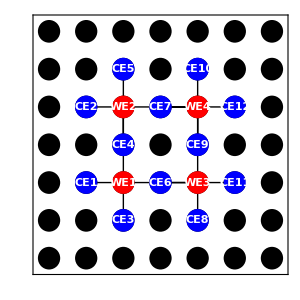

```mathematica
p0=Graphics[{Line[#]&/@Table[Flatten[MapThread[{#1,#2}&,{ConstantArray[CE[[i]],Length@neighbourlistWE[[i]]],neighbourlistWE[[i]]}],1],{i,Length@CE}],Flatten[Table[Disk[{i,j},0.3],{i,nEl},{j,nEl}],1],Flatten[{Red,Disk[#,0.3]}&/@WE],Flatten[{Blue,Disk[#,0.3]}&/@CE],White,Table[Text[Style["WE"<>ToString[i],Bold],WE[[i]]],{i,Length@WE}],Table[Text[Style["CE"<>ToString[i],Bold],CE[[i]]],{i,Length@CE}]},ImageSize->300,Frame->True,FrameTicks->None,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"Electrode_Layout.png",p0,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\Electrode_Layout.png

```mathematica
updateStates[states_]:=Block[{newStates},newStates=states+RandomVariate[NormalDistribution[0,noiseMax],Length@nS];Piecewise[{{1,#>1},{0,#<0}},#]&/@newStates]
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
```

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,stateAbs,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl->CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;Vapp={}; solnS={}; 

(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;

(* Initializing abstract states and equivalent pH states *)
initStates =RandomReal[{0,1},Length@nS]; (* Setting initial abstract space *)
stateAbs=initStates;
initpH=(pHStateMin+(pHStateMax-pHStateMin)(#))&/@initStates;
setpHe=initpH; (* Setting initial pH states *)
PrintTemporary["Initial Abstract space : ",stateAbs];
PrintTemporary["Initial pH states : ",initpH];

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];

WriteLine[logFile,"-------------------------------------------------------------"];
WriteLine[logFile,"Current Switching Step : "<>ToString[ cnTs]<> "; Current Time : "<> ToString[cnTs tS]];

(* Randomly selecting pH states on all working electrodes *)
If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],
(* Update Abstract states *)
stateAbs=updateStates[stateAbs];
(* Update pH states *)
setpHe=(pHStateMin+(pHStateMax-pHStateMin)(#))&/@stateAbs;
(*
pHstates= RandomChoice[{-1,1},Length[WE]];
setpHe=Table[If[pHstates⟦i⟧== 1,pHstate1,pHstate2]
,{i,Length[WE]}];
*)
PrintTemporary["****** SWITCHING TO NEW STATES ******"]];PrintTemporary["Current abstract computational states : ", stateAbs];
PrintTemporary["Current pH states : ", setpHe];
(*
WriteLine[logFile,"Current abstract computational states : "<>ToString[pHstates]];
WriteLine[logFile,"Current pH states : "<>ToString[setpHe]];
*)

Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];
PrintTemporary[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}]];
dim=Dimensions[currentEL]; 
PrintTemporary[dim];
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
PrintTemporary["pH state STATUS : ",If[Abs[pHdiff⟦#⟧]≤ stateRange/2. ,"A","NA"]&/@Range[Length[pHdiff]]];

WriteLine[logFile,"Current Measured pHs : "<>ToString[NumberForm[currentpH,3]]];
WriteLine[logFile,"Current pH differences : "<>ToString[NumberForm[pHdiff,3]]];
WriteLine[logFile,"pH state STATUS : "<>ToString[If[Abs[pHdiff⟦#⟧]≤ stateRange/2. ,"A","NA"]&/@Range[Length[pHdiff]]]];
cnTs=cnTs+1]];
```

Running Simulation

```mathematica
cnTs=0;nSteps=100;
electroChemAutomata[nEl,nSteps]
```

```mathematica
Dimensions@dataT
```

{101,7,7,41,5}

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.005],Length@WE],ConstantArray[Opacity[0.4],Length@WE],ColorData[16,#]&/@Range[Length@WE]}];
```

```mathematica
timeList=Range[0.1,(nSteps +1)tS ,timeStep];
```

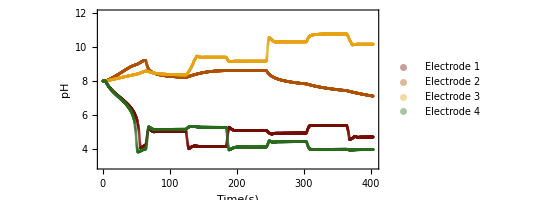

```mathematica
p1=ListPlot[Table[MapThread[{#1,#2}&,{timeList,Flatten[(dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧,1;;IntegerPart@(tS/timeStep)⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,4}],PlotStyle->plotStyle,AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time(s)","pH"},PlotRange-> {All,{3,12}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.15,0.8}],ImageSize->400]
```

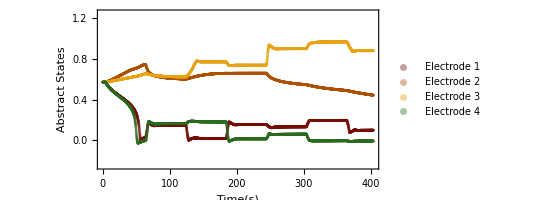

```mathematica
p2=Block[{data=Table[Flatten[(dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧,1;;IntegerPart@(tS/timeStep)⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧,{i,1,4}],dataX},
dataX=(1/(pHStateMax-pHStateMin) (#-pHStateMin))&/@data;
ListPlot[Table[MapThread[{#1,#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,FrameLabel-> {"Time(s)","Abstract States"},PlotRange-> {All,{-0.25,1.25}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.15,0.8}],ImageSize->400]]
```

```mathematica
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
```

```mathematica
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0.1,nSteps tS,0.1}];
dataX=Table[voltageData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

```mathematica
timeList=Range[0.1,nSteps tS ,timeStep];
```

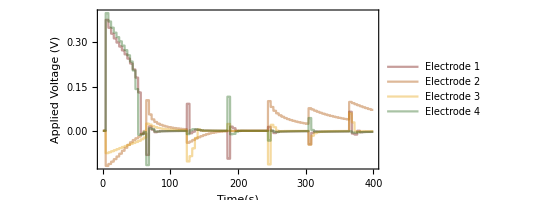

```mathematica
p3=ListPlot[Table[MapThread[{#1,#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.75}],ImageSize->400]
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC];
```

```mathematica
currentData=Table[plotCurrent[nEl,time],{time,0.1,nSteps tS,0.1}];
dataX=Table[currentData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

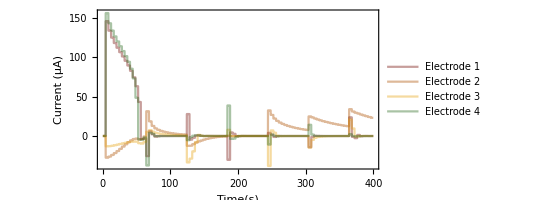

```mathematica
p4=ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.8,0.75}],ImageSize->400]
```

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.005],Length@CE],ConstantArray[Opacity[0.2],Length@CE],ColorData[10,#]&/@Range[Length@CE]}];
```

```mathematica
dataX=Table[currentData[[All,CE[[i,1]],CE[[i,2]]]],{i,Length@CE}];
```

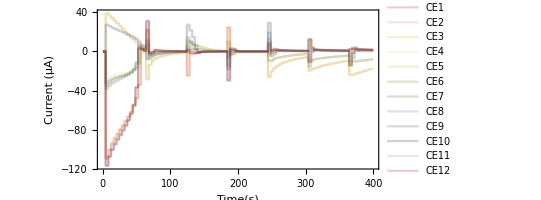

```mathematica
p5=ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@CE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[Table["CE"<>ToString[el],{el,Length@CE}],LabelStyle->12,LegendLayout->"Row",Spacings-> {0.15,0.15}],{0.5,0.15}],ImageSize->400]
```

```mathematica
Export[baseDirectory<>"RandomTraj_4_11_1.png",p1,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\RandomTraj_4_11_1.png

```mathematica
Export[baseDirectory<>"RandomTraj_4_11_2.png",p2,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\RandomTraj_4_11_2.png

```mathematica
Export[baseDirectory<>"RandomTraj_4_11_3.png",p3,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\RandomTraj_4_11_3.png

```mathematica
Export[baseDirectory<>"RandomTraj_4_11_4.png",p4,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\RandomTraj_4_11_4.png

```mathematica
Export[baseDirectory<>"RandomTraj_4_11_5.png",p5,ImageResolution->300]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\RandomTraj_4_11_5.png

```mathematica
BL1=BarLegend[{"TemperatureMap",{-1.,1.}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Applied Voltage (V)",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL2=BarLegend[{"TemperatureMap",{-0.5,0.5}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Electrode Current(mA)",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL3=BarLegend[{"Pastel",{0,0.2}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL4=BarLegend[{"LightTemperatureMap",{3,12}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "pH",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
BL5=BarLegend[{"TemperatureMap",{0,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},LegendLabel-> "QUBO States",LegendLayout->"Row",LegendLayout->"Row",LegendFunction->"Frame",LegendMargins->10]
```

```mathematica
Export[baseDirectory<>"BL_AppliedVoltage.svg",BL1]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\BL_AppliedVoltage.svg

```mathematica
Export[baseDirectory<>"BL_ElectrodeCurrent.svg",BL2]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\BL_ElectrodeCurrent.svg

```mathematica
Export[baseDirectory<>"BL_InterfaceCurrent.svg",BL3]
```

Z:\group\0-Papers in Progress\Hybrid_Computation_Abhishek\Hybrid_Computation_Final_ToSubmit\BL_InterfaceCurrent.svg

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-1.,1.}}][k]; (* Applied Potential *)
state1[k_]:=ColorData[{"TemperatureMap",{-1 10^-4,1 10^-4}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"Pastel",{0,1 10^-4}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"TemperatureMap",{3,12}}][k]; (* pH profile *)
state4[k_]:= ColorData[{"TemperatureMap",{0,1}}][k];(* QUBO States *)
```

```mathematica
(* Plots applied voltage at a given time *)
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl];
Graphics[Flatten@Table[{stateV[plotV⟦i,j⟧],Disk[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Applied Potential",FontSize->14,FontColor->Black]]]];
```

```mathematica
(* Plots electrode current magnitude at a given time *)
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC;
Graphics[Flatten@Table[{state1[currentEL⟦i,j⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
(* Plots interfacial current magnitude at a given time *)
plotCurrentCon[nEl_,tC_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t] }/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten[{Table[{state2[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state2[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],Table[{state2[Abs[dataPlot2⟦i,3⟧]],Rectangle[{2dataPlot2⟦i,1⟧-0.45-1,2dataPlot2⟦i,2⟧-0.45},{2dataPlot2⟦i,1⟧+0.45-1,2dataPlot2⟦i,2⟧+0.45}]},{i,1,nEl}],Table[{state2[Abs[dataPlot3⟦i,3⟧]],Rectangle[{1+2dataPlot3⟦i,1⟧-0.45-1,2dataPlot3⟦i,2⟧-0.45-1},{1+2dataPlot3⟦i,1⟧+0.45-1,2dataPlot3⟦i,2⟧+0.45-1}]},{i,1,nEl}]}],PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]],ImageSize->300]];
```

```mathematica
(* Plots current/electric fields vectors at a given time *)
plotCurrentVec[nEl_,tC_,color_]:=Block[{cnT, time,dataPlot,dataPlot2,dataPlot3},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
dataPlot2=(Table[{1,j,Symbol["iCW1"<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{j,nEl}])/.t-> tC;
dataPlot3=(Table[{i,1,Symbol["iCS"<>ToString[i]<>"s"<>"1"][t]}/.solnS⟦cnT⟧,{i,nEl}])/.t-> tC;
Graphics[Flatten@{color,If[dataPlot⟦#,3⟧≥0,Arrow[{{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧}}],Arrow[{{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧}}]]&/@Range[nEl^2],
If[dataPlot⟦#,4⟧≥0,Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45}}],Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45}}]]&/@Range[nEl^2],
If[dataPlot2⟦#,3⟧≥0,Arrow[{{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧}}],Arrow[{{2dataPlot2⟦#,1⟧+0.45-1,2dataPlot2⟦#,2⟧},{2dataPlot2⟦#,1⟧-0.45-1,2dataPlot2⟦#,2⟧}}]]&/@Range[nEl],
If[dataPlot3⟦#,3⟧≥0,Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1}}],Arrow[{{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧+0.45-1},{2dataPlot3⟦#,1⟧,2dataPlot3⟦#,2⟧-0.45-1}}]]&/@Range[nEl]
},ImageSize->300]];
```

```mathematica
(*Plots pH of the droplets at a given time,fixed time step 0.1s*)plotpH[tC_]:=Block[{data},data=Flatten[Table[dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧⟦i,All,1⟧,{i,1,nSteps}],1]&/@Range[Length[WE]];
Graphics[Flatten[{Table[{state3[data⟦i,tC⟧],Disk[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.45],Black,Circle[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.9]},{i,Length[WE]}],Table[{Black,Circle[{2 i,2 j},0.45],Black,Circle[{2 i,2 j},0.9]},{i,nEl},{j,nEl}]}],ImageSize->300,Frame->True,FrameTicks->None,PlotLabel->Text[Style["pH ",FontSize->14,FontColor->Black]]]]
```

```mathematica
plotAbstractState[tC_]:=Block[{data,dataX},data=Flatten[Table[dataT⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧⟦i,All,1⟧,{i,1,nSteps}],1]&/@Range[Length[WE]];
dataX=((#-pHStateMin)/(pHStateMax-pHStateMin))&/@data;Graphics[Flatten[{Table[{state4[dataX⟦i,tC⟧],Disk[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.45],Black,Circle[{2 WE⟦i,1⟧,2 WE⟦i,2⟧},0.9]},{i,Length[WE]}],Table[{Black,Circle[{2 i,2 j},0.45],Black,Circle[{2 i,2 j},0.9]},{i,nEl},{j,nEl}]}],ImageSize->300,Frame->True,FrameTicks->None,PlotLabel->Text[Style["Abstract state ",FontSize->14,FontColor->Black]]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsGrid[Partition[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t]},Frame->True,FrameTicks->None],plotpH[IntegerPart[t/timeStep]],plotAbstractState[IntegerPart[t/timeStep]]},2],Frame->All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]],ImageSize->400]
```

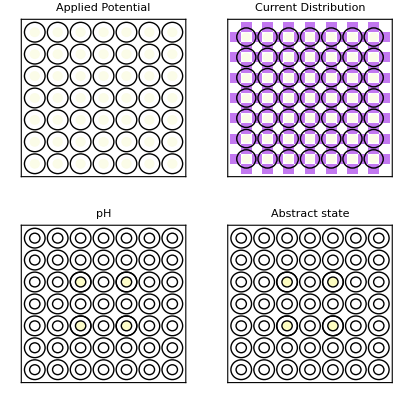

```mathematica
plot[nEl,1.5]
```

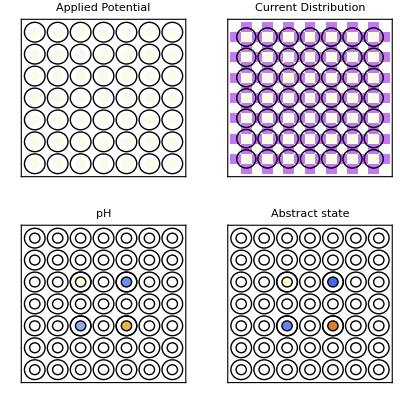

-Graphics-

-Graphics-

```mathematica
plot[nEl,300]
```